# Plotting phase

## Input

tablepaper includes the average phases and the visibility, tablehistogram1 includes the phase distribution histogram

```mathematica
tablepaper=Import[NotebookDirectory[]<>"plotting_phasespaper_pi_4.txt","Table"];
tablehistogram1=Import[NotebookDirectory[]<>"whistrogram_paperpi_4.txt","Table"];
thetam=Pi/4.;
```

## Plotting phase

#### post selected phase

phase of the post-selected trajectory, with the analytical formula given in the main text

```mathematica
zett=const+ⅈ*Pi*Cos[thetam];
tau=Sqrt[zett^2-Pi^2*Sin[thetam]^2];
paperplot=LogLinearPlot[Arg[-(Cosh[tau]+zett*Sinh[tau]/tau)]
,{const,0.001,500},PlotStyle->{Thickness[.007],Red}];
```

#### histogram

Construction of the histogram, with definition of the colors

```mathematica
max=3000;
mind=1.1;
colors1=tablehistogram1;
For[i=1,i<Length[tablehistogram1[[;;,1]]]+1,i++,
For[j=1,j<Length[tablehistogram1[[1,;;]]]+1,j++,
colors1[[i]][[j]]=Directive[GrayLevel[0,HeavisideTheta[tablehistogram1[[i]][[j]]-mind]*(1-.985*(Rescale[tablehistogram1[[i]][[j]],{0,max}]-1)^4)],PointSize[.015]]]
]
valueconst=tablepaper[[;;,1]];
res=Length[tablehistogram1[[1]]];
datahistogram1=Table[{valueconst[[i]],-Pi+2*Pi*(j-1)/res},{i,1,Length[valueconst]},{j,1,res}];
datahistogramnew1={#}&/@(Flatten[datahistogram1,1]);
pointplot1=ListLogLinearPlot[datahistogramnew1,PlotStyle->Flatten[colors1,1],PlotMarkers->■];
```

#### produce and export figure

Combine average phase , post-selected phase and phase histogram in one figure

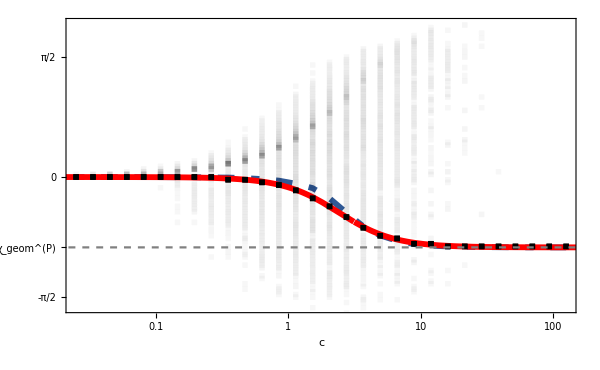

```mathematica
picturephasepaper3=Show[{ListLogLinearPlot[Transpose[{tablepaper[[All,1]],tablepaper[[All,6]]}],Joined->True,PlotStyle->{{RGBColor[0.19, 0.35000000000000003, 0.59],Thickness[.007],Dashing[{0.01,.02,.02,.02}]}},Frame->True,FrameLabel->{"c",None},FrameTicks->{{{0,{-Pi(1-Cos[Pi/4]),Subscript[χ, "geom"]^("(P)")},-Pi/2,Pi/2},None},{Table[{10^k,Superscript[10,k]},{k,-4,4}],None}},FrameStyle->{FontFamily->"Minion Pro Med",FontSize->22},ImageSize->Large,FrameStyle->Black,BaseStyle->{Black,FontFamily->"Minion Pro Med",FontSize->22},LabelStyle->Directive[FontFamily->"Calibri",FontSize->24,Black,FractionBoxOptions->{Beveled->True}],ImagePadding->All,PlotRange->{{.025,125},{-1.7,2.0}}](*,ListLogLinearPlot[Transpose[datanihal]]*),paperplot,pointplot1,Plot[-Pi(1-Cos[Pi/4]),{c,-10,100},PlotStyle->{Dashed,Gray}]},ImageSize->600]
(*figurepath ="/Users/freygebhart/Dropbox/WIS/python/mycode/";
Export[figurepath<>"phase_paper_m500N4000.png",picturephasepaper3]*)
```

Legend for histogram

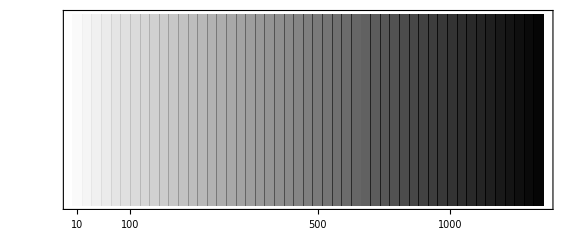

```mathematica
rec={};
For[k=1,k<50,k++,
AppendTo[rec,{GrayLevel[0,k/50],Rectangle[{k/50,0},{(k+1)/50,.15}]}]
]
legend=Graphics[rec,ImageSize->Large,Frame->True,FrameTicks->{{None,None},{{{.028,10},{.14,100},{.805,1000},{.53,500}},None}},FrameStyle->{FontFamily->"Minion Pro Med",FontSize->30},LabelStyle->Black]
```

## Plotting visibility

#### post selected probability

Probability of the post-selected trajectory, with analytical formula as given in the main text

```mathematica
zett=const+ⅈ*Pi*Cos[thetam];
tau=Sqrt[zett^2-Pi^2*Sin[thetam]^2];
paperplot2=LogLinearPlot[Abs[-Exp[-const]*(Cosh[tau]+zett*Sinh[tau]/tau)]^2
,{const,0.001,500},PlotStyle->{Red, Thickness[0.02]},Frame->True,FrameLabel->{"c","\!\(\*
StyleBox[\"P\",\nFontColor->RGBColor[1, 0, 0]]\)"<>" and "<>"\!\(\*
StyleBox[\"e^-α\",\nFontColor->RGBColor[0.19, 0.35, .59]]\)"},FrameTicks->{{{0,1},None},{Table[{10^k,Superscript[10,k]},{k,-4,4}],None}},FrameStyle->{FontFamily->"Minion Pro Med",FontSize->22},ImageSize->Large,FrameStyle->Black,LabelStyle->Black,BaseStyle->{Black,FontFamily->"Minion Pro Med",FontSize->22},LabelStyle->Directive[FontFamily->"Calibri",FontSize->24,Black,FractionBoxOptions->{Beveled->True}],ImagePadding->All,PlotRange->{{.025,125},{0,1.1}}];
```

#### produce and export figure

Plot of the visibility of the phase together with the probability of the post-selected trajectory

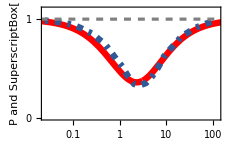

```mathematica
prob=Array[0&,Length[tablepaper[[All,1]]]];
For[k=1,k<Length[tablepaper[[All,1]]]+1,k++,
prob[[k]]={tablepaper[[k,1]],tablepaper[[k,8]]}]
pictureprobpaper=Show[paperplot2,ListLogLinearPlot[prob,Joined->True,PlotStyle->{{RGBColor[0.19, 0.35000000000000003, 0.59],Thickness[.02],Dashing[{0.011,.02,.02,.02}]}}](*,ListLogLinearPlot[Transpose[datanihalprob]]*),Plot[1,{c,-10,100},PlotStyle->{Gray,Dashed,Thickness[0.01]}],ImageSize->230]
(*figurepath ="/Users/freygebhart/Dropbox/WIS/python/mycode/";
Export[figurepath<>"prob_paper_m500N4000.png",pictureprobpaper]*)
```